```mathematica
G=6.7*^-11;
mPluto=1.305*^22;
mCharon=1.52*^21;
a=17536000;
Plot3D[
-G(mPluto/Norm[{x,y}]+mCharon/Norm[{x-a,y}]),
{x,-.2a,1.2a},
{y,-.7a,.7a},
PlotPoints->100,
AxesLabel->Thread[Style[{x,y,V},Large]]
]
```

-Graphics3D-

```mathematica
G=6.7*^-11;
mPluto=1.305*^22;
mCharon=1.52*^21;
a=17536000;
Manipulate[
Plot3D[
-G(mPluto/Norm[{x,y}]+mCharon/Norm[{x-a,y}]),
{x,-.2a,1.2a},
{y,-.7a,.7a},
PlotPoints->100,
AxesLabel->Thread[Style[{x,y,V},Large]],
PlotRange->{H,H+500000}
],
{H,-300000,0}
]
```

```mathematica
Plot3D[
{
-G(mPluto/Norm[{x,y}]+mCharon/Norm[{x-a,y}]),
},
{x,-2a,2a},
{y,-2a,2a},
AxesLabel->Thread[Style[{x,y,V},Large]],
PlotRange->{-500000,0},
PlotPoints->75,
ImageSize->500,
PlotStyle->{
Directive[Blend[{Yellow,Orange},.5],Specularity[White,50]]
},
Lighting->{{"Directional",RGBColor[1,1,1],{{0,0,.2},{5,5,0}}}}
]
```

-Graphics3D-

```mathematica
q0={-1500000,0};
p0={0,1000};
T=60 60 24 1;
Q=First[
{x,y}/.NDSolve[{
{x''[t],y''[t]}==-G({x[t],y[t]}mPluto/Norm[{x[t],y[t]}]^3+{x[t]-a,y[t]}mCharon/Norm[{x[t]-a,y[t]}]^3),
{x[0],y[0]}==q0,
{x'[0],y'[0]}==p0
},{x,y},{t,0,T},
StartingStepSize->1,
MaxStepSize->10,
MaxSteps->100000,
Method->{"SymplecticPartitionedRungeKutta","PositionVariables"->{x,y}}
]
];
q=Function[t,{Q⟦1⟧[t],Q⟦2⟧[t]}];
```

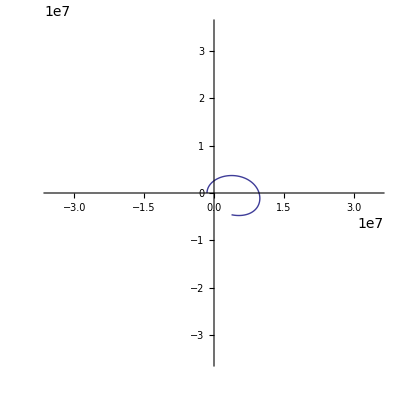

```mathematica
ParametricPlot[q[t],{t,0,T},PlotRange->{{-2a,2a},{-2a,2a}}]
```

```mathematica
TableForm[
ArrayReshape[
Table[
q0={-1500000,0};
V0=-G(mPluto/Norm[q0]+mCharon/Norm[q0-{a,0}]);
𝒯=H-V0;
p0={0,√(2𝒯)};
T=60 60 24 2;
Q=First[
{x,y}/.NDSolve[{
{x''[t],y''[t]}==-G({x[t],y[t]}mPluto/Norm[{x[t],y[t]}]^3+{x[t]-a,y[t]}mCharon/Norm[{x[t]-a,y[t]}]^3),
{x[0],y[0]}==q0,
{x'[0],y'[0]}==p0
},{x,y},{t,0,T},
StartingStepSize->1,
MaxStepSize->100,
MaxSteps->200000,
Method->{"SymplecticPartitionedRungeKutta","PositionVariables"->{x,y}}
]
];
q=Function[t,{Q⟦1⟧[t],Q⟦2⟧[t],H}];
Show[
Plot3D[
{
-G(mPluto/Norm[{x,y}]+mCharon/Norm[{x-a,y}]),
H
},
{x,-2a,2a},
{y,-2a,2a},
AxesLabel->Thread[Style[{x,y,V},Large]],
PlotRange->{-500000,0},
PlotPoints->75,
ImageSize->500,
PlotStyle->{
Directive[Blend[{Yellow,Orange},.5],Specularity[White,50]],
Directive[Opacity[0.6],Blue,Specularity[White,50]]
},
Lighting->{{"Directional",RGBColor[1,1,1],{{0,0,.2},{5,5,0}}}}
],
ParametricPlot3D[q[t],{t,0,T},PlotStyle->Red]
],
{H,-150000,0,20000}
],
{3,3},
""
]
]
```

-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- |